# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

NAIVE ANTICOMMUTING {GAMMA5,GAMMA_mu}=0 
 massless MM=0

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
Neglect[MM] = Neglect[MM2] = 0;
process ={-F[3, {1}], F[3, {1}]} -> {-F[2, {2}], F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];
SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams



FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

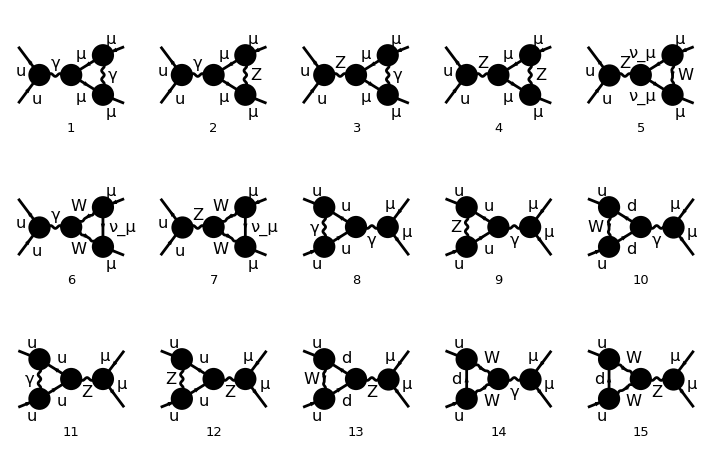

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

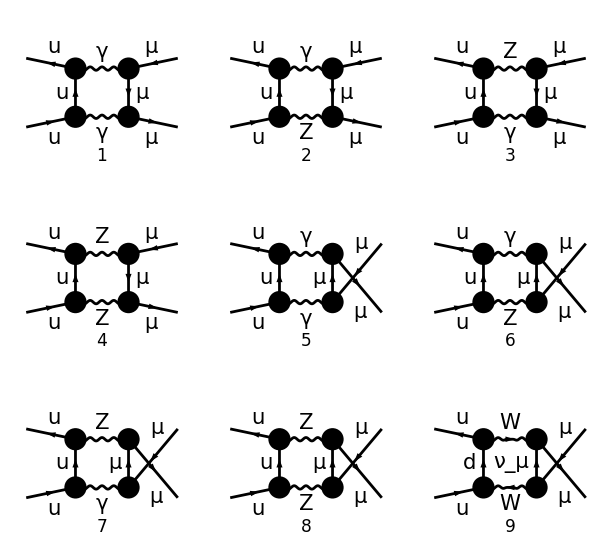

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

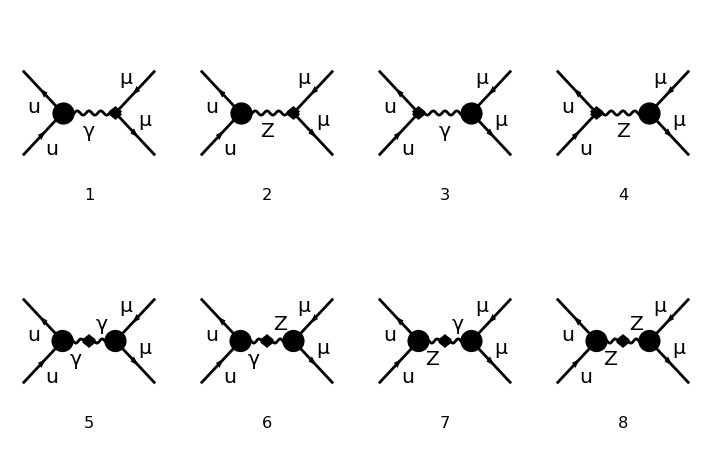

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

ampiezzabox . ampiezzaborn*

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];

boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]},
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)
{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{γ,Z}},{3,T,{Z,γ}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{γ,Z}},{7,U,{Z,γ}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={γ,Z},{2,6}},{couple[3]=={Z,γ},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

```mathematica
Table[tboxzz[i]=verttt[[i,3]]//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]},{i,1,15}];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i] e 1 per fotone e 2 per z per born diagram

```mathematica
(*funzione per semplificare propagatori*)
numer[x__ PropagatorDenominator[p_,MZ] PropagatorDenominator[p_,mzg]]:=numer[x/(MZ^2-mzg^2)(PropagatorDenominator[p,MZ]-PropagatorDenominator[p,mzg])];
numerw[x__ PropagatorDenominator[p_,MW] PropagatorDenominator[p_,mwg]]:=numerw[x/(MW^2-mwg^2)(PropagatorDenominator[p,MW]-PropagatorDenominator[p,mwg])];
```

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P1],x_]->DiracSpinor[P1,x],DiracSpinor[Times[-1,K1],x_]->DiracSpinor[K1,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p2,0].(ⅈ EL QUl ga[Lorbn1].om_-+ⅈ EL QUr ga[Lorbn1].om_+).u[p1,0]],CONJ[ū[k1,0].(ⅈ EL QLl ga[Lorbn2].om_-+ⅈ EL QLr ga[Lorbn2].om_+).v[k2,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz[1]]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

#### Propagators

```mathematica
(*box t*)
Table[tnumerat[i]=DeleteCases[tboxzz[i], _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//Simplify,{i,1,15}];
```

```mathematica
propag=Table[tnumerat[i]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2),{i,1,15}];
```

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)

myTr[a_,b_] := 4 SP[a,b];

myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}
                                        ];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato

  ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;

myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] = -4 I myEps[a1,a2,a3,a4];

myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 

  risultato

  ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;

(*myTr[a___,{mu_},{mu_}, b___] := d myTr[a,b];
myTr[a___,{mu_},b__,{mu_},c___] := (-1)^Length[{b}] d myTr[a,b,c] + 
Sum[ ma={b}; tmp=Delete[ma,i]; 
     (-1)^(i+1) 2 SP[ ma[[i]], {mu}] myTr[a, Sequence @@ tmp, c],
       {i,1,Length[{b}]}   ]; *)
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=0;
SP/:SP[K1,K1]:=0;
```

```mathematica
SP/: SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2;
 SP/:SP[P1,K1]:=(-T)/2; 
SP/:SP[P2,K2]:=(-T)/2;
SP/: SP[P1,K2]:=(-U)/2; SP/:SP[P2,K1]:=(-U)/2
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
move2[a___,1,b___]:=move2[a,b];
move2[a___,-G5,b___]:=-move2[a,G5,b];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{tr1i,tr2i,tr3i,tr1f,tr2f,tr3f,tracciai,tracciaf},

(*trace:*)
traceff[x___, DiracSpinor[z_,w_], DiracSpinor[z_,w_],y___]:=traceff[x,(DiracSlash[z]+w),y];(* ...u(p)u_bar(p) ... -> ...p_slash... *)(*sost. stato intermedio*)
traceff[ DiracSpinor[z_,w_],x__,DiracSpinor[z_,w_]]:=traceff[(DiracSlash[z]+w),x];(* v_bar(p)...v(p) ->p_slash... *)(*sost. stato esterno*)

(*stato i*)
tr1i=Table[traceff[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff->move2;(*sposto proiettori in fondo*)
tr2i=Map[Distribute,1/2 DeleteCases[tr1i*chi,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=tr2i//.move2->myTr/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;(*espando e calcolo traccia*)
tracciai=tr3i/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]}//.{myEps[a___,DiracMatrix[b__],c___]:>myEps[a,b,c],myEps[a___,DiracSlash[b__],c___]:>myEps[a,b,c]}//.List->Plus//Expand;


(*stato f*)
tr1f=Table[traceff[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[Distribute[tr1f[[i]]],{i,1,Length[tr1f]}],Plus->Sequence,{2},Heads->True]//.traceff->move2;
tr2f=Map[Distribute,1/2 DeleteCases[tr1f*chf,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];
tr3f=tr2f//.move2->myTr/.{DiracMatrix->Sequence,DiracSlash->Sequence}//Expand;
tracciaf=DeleteCases[tr3f/.{ SP[a_,b_]:>Distribute[SP[a,b]], myEps[a_,b__]:>Distribute[myEps[a,b]]},0]//.{myEps[a___,DiracMatrix[b__],c___]:>myEps[a,b,c],myEps[a___,DiracSlash[b__],c___]:>myEps[a,b,c]}//.List->Plus//Expand;

Print["stato i ",1/2 DeleteCases[tr1i,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},"\n stato f ",
1/2 DeleteCases[tr1f,0,1]//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];


Return[{tracciai,tracciaf}]

];
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
sostituzione={SP[P2,P2]->0,SP[P1,P1]->0,SP[K2,K2]->0,SP[K1,K1]->0,SP[Q1,Q1]->Q1^2,
 SP[P1,P2]->S/2, SP[K1,K2]->S/2, SP[P1,K1]->(-T)/2, SP[P2,K2]->(-T)/2, SP[P1,K2]->(-U)/2, SP[P2,K1]->(-U)/2};
```

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c},
(*****BORN*****)
tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

```mathematica
Table[vertic[i]=traces[fermiontrace[tboxzz[i]][[1]],fermiontrace[tboxzz[i]][[2]]]//Expand,{i,1,15}];
```

## Semplificazioni/sostituzioni

```mathematica
eps=Table[Select[vertic[j][[1]],MemberQ[#,_myEps,Infinity]&]*Select[vertic[j][[2]],MemberQ[#,_myEps,Infinity]&]//Expand,{j,1,15}];
```

```mathematica
neps=Table[Select[vertic[j][[1]],FreeQ[#,_myEps,Infinity]&]*Select[vertic[j][[2]],FreeQ[#,_myEps,Infinity]&]//Expand,{j,1,15}];
```

```mathematica
vveps=ParallelTable[eps[[i]]*bornpropag2*propag[[i]]//.denominators//Expand,{i,1,15}];
```

```mathematica
vvneps=ParallelTable[neps[[i]]*bornpropag2*propag[[i]]//.denominators//Expand,{i,1,15}];
```

```mathematica
ampl=ParallelTable[Collect[vveps[[i]]+vvneps[[i]]//.{K2^2->0,K1^2->0,P1^2->0,P2^2->0,K1*K2->S/2}//.SP[n_*p_,q_]->n *SP[p,q]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2},SP[__],Simplify],{i,1,15}];
```

```mathematica
Collect[ampl[[3]]//.d->4-2ϵ,ϵ,Simplify]
```

-((ⅈ el^6 QL^3 QU ϵ^2 (2 I3L I3U S T^2-2 I3L I3U S U^2+I3L I3U S^2 SP[q1,q1]-2 I3U QL S^2 SW2 SP[q1,q1]-2 I3L QU S^2 SW2 SP[q1,q1]+4 QL QU S^2 SW2^2 SP[q1,q1]-I3L I3U T^2 SP[q1,k1]+I3L I3U U^2 SP[q1,k1]+2 I3L I3U T^2 SP[q1,k2]-2 I3L I3U U^2 SP[q1,k2]+I3L I3U SP[p2,q1] (3 S T+2 S U-4 U SP[q1,k1]+4 T SP[q1,k2])-I3L I3U SP[p1,q1] (2 S T+3 S U-4 T SP[q1,k1]+4 U SP[q1,k2])))/(4 CW2 π^4 SW2 dn[1] dn[6] dn[11] dn[14] dn[16]))-(ⅈ el^6 QL^3 QU ϵ (2 I3L I3U S^3-4 I3U QL S^3 SW2-4 I3L QU S^3 SW2+8 QL QU S^3 SW2^2-6 I3L I3U S T^2+6 I3L I3U S U^2-2 I3L I3U T^2 SP[q1,q1]+4 I3U QL SW2 T^2 SP[q1,q1]+4 I3L QU SW2 T^2 SP[q1,q1]-8 QL QU SW2^2 T^2 SP[q1,q1]-2 I3L I3U U^2 SP[q1,q1]+4 I3U QL SW2 U^2 SP[q1,q1]+4 I3L QU SW2 U^2 SP[q1,q1]-8 QL QU SW2^2 U^2 SP[q1,q1]-4 I3L I3U S^2 SP[q1,k1]+8 I3U QL S^2 SW2 SP[q1,k1]+8 I3L QU S^2 SW2 SP[q1,k1]-16 QL QU S^2 SW2^2 SP[q1,k1]+5 I3L I3U T^2 SP[q1,k1]-5 I3L I3U U^2 SP[q1,k1]+4 I3L I3U S^2 SP[q1,k2]-8 I3U QL S^2 SW2 SP[q1,k2]-8 I3L QU S^2 SW2 SP[q1,k2]+16 QL QU S^2 SW2^2 SP[q1,k2]-6 I3L I3U T^2 SP[q1,k2]+6 I3L I3U U^2 SP[q1,k2]-8 I3L I3U S SP[q1,k1] SP[q1,k2]+16 I3U QL S SW2 SP[q1,k1] SP[q1,k2]+16 I3L QU S SW2 SP[q1,k1] SP[q1,k2]-32 QL QU S SW2^2 SP[q1,k1] SP[q1,k2]+SP[p2,q1] (-I3L I3U S (7 T+6 U)+8 (QL SW2 (I3U-2 QU SW2)+I3L (I3U+QU SW2)) U SP[q1,k1]-8 (2 I3L I3U-I3U QL SW2-I3L QU SW2+2 QL QU SW2^2) T SP[q1,k2])+SP[p1,q1] (6 I3L I3U S T+7 I3L I3U S U-8 S (I3L-2 QL SW2) (I3U-2 QU SW2) SP[p2,q1]-8 (2 I3L I3U-I3U QL SW2-I3L QU SW2+2 QL QU SW2^2) T SP[q1,k1]+8 I3L I3U U SP[q1,k2]+8 I3U QL SW2 U SP[q1,k2]+8 I3L QU SW2 U SP[q1,k2]-16 QL QU SW2^2 U SP[q1,k2])))/(8 CW2 π^4 SW2 dn[1] dn[6] dn[11] dn[14] dn[16])+(ⅈ el^6 QL^3 QU (-2 I3U QL S SW2 T^2-2 I3L QU S SW2 T^2+4 QL QU S SW2^2 T^2+2 I3L I3U S U^2-2 I3U QL S SW2 U^2-2 I3L QU S SW2 U^2+4 QL QU S SW2^2 U^2+I3L I3U S^2 SP[q1,q1]-2 I3U QL S^2 SW2 SP[q1,q1]-2 I3L QU S^2 SW2 SP[q1,q1]+4 QL QU S^2 SW2^2 SP[q1,q1]-I3L I3U T^2 SP[q1,q1]+2 I3U QL SW2 T^2 SP[q1,q1]+2 I3L QU SW2 T^2 SP[q1,q1]-4 QL QU SW2^2 T^2 SP[q1,q1]-I3L I3U U^2 SP[q1,q1]+2 I3U QL SW2 U^2 SP[q1,q1]+2 I3L QU SW2 U^2 SP[q1,q1]-4 QL QU SW2^2 U^2 SP[q1,q1]+2 I3U QL SW2 T^2 SP[q1,k1]+2 I3L QU SW2 T^2 SP[q1,k1]-4 QL QU SW2^2 T^2 SP[q1,k1]-2 I3L I3U T U SP[q1,k1]+4 I3U QL SW2 T U SP[q1,k1]+4 I3L QU SW2 T U SP[q1,k1]-8 QL QU SW2^2 T U SP[q1,k1]-2 I3L I3U U^2 SP[q1,k1]+2 I3U QL SW2 U^2 SP[q1,k1]+2 I3L QU SW2 U^2 SP[q1,k1]-4 QL QU SW2^2 U^2 SP[q1,k1]-2 I3U QL SW2 T^2 SP[q1,k2]-2 I3L QU SW2 T^2 SP[q1,k2]+4 QL QU SW2^2 T^2 SP[q1,k2]+2 I3L I3U T U SP[q1,k2]-4 I3U QL SW2 T U SP[q1,k2]-4 I3L QU SW2 T U SP[q1,k2]+8 QL QU SW2^2 T U SP[q1,k2]+2 I3L I3U U^2 SP[q1,k2]-2 I3U QL SW2 U^2 SP[q1,k2]-2 I3L QU SW2 U^2 SP[q1,k2]+4 QL QU SW2^2 U^2 SP[q1,k2]-4 I3L I3U S SP[q1,k1] SP[q1,k2]+8 I3U QL S SW2 SP[q1,k1] SP[q1,k2]+8 I3L QU S SW2 SP[q1,k1] SP[q1,k2]-16 QL QU S SW2^2 SP[q1,k1] SP[q1,k2]-2 SP[p2,q1] (S (I3U QL SW2 (T-U)+QU SW2 (I3L-2 QL SW2) (T-U)+I3L I3U U)-2 SW2 (I3U QL+QU (I3L-2 QL SW2)) U SP[q1,k1]+2 (I3L (I3U-QU SW2)+QL SW2 (-I3U+2 QU SW2)) T SP[q1,k2])+2 SP[p1,q1] (I3U QL S SW2 T+I3L QU S SW2 T-2 QL QU S SW2^2 T+I3L I3U S U-I3U QL S SW2 U-I3L QU S SW2 U+2 QL QU S SW2^2 U-2 S (I3L-2 QL SW2) (I3U-2 QU SW2) SP[p2,q1]+2 (QL SW2 (I3U-2 QU SW2)+I3L (-I3U+QU SW2)) T SP[q1,k1]+2 I3U QL SW2 U SP[q1,k2]+2 I3L QU SW2 U SP[q1,k2]-4 QL QU SW2^2 U SP[q1,k2])))/(4 CW2 π^4 SW2 dn[1] dn[6] dn[11] dn[14] dn[16])

```mathematica
dn1=1/Union[Replace[Table[Select[Denominator[propag[[i]]*bornpropag2],MemberQ[#,FourMomentum,Infinity,Heads->True]&],{i,1,15}],Times->Sequence,{2},Heads->True]]
denominators=Table[dn1[[i]]->1/dn[i],{i,1,Length[dn1]}]
denominatorsINV=Table[1/dn[i]->dn1[[i]],{i,1,Length[dn1]}];
```

{1/(q1)^2,1/(p2+q1)^2,1/(-MW2+(q1)^2),1/(-MZ2+(q1)^2),1/(-MW2+(p2+q1)^2),1/(q1+k1)^2,1/(-MW2+(q1+k1)^2),1/(-MW2+(q1-k2)^2),1/(-MZ2+(-(k1)-k2)^2),1/(-MW2+(p2+q1-k1-k2)^2),1/(q1-k2)^2,1/(-(k1)-k2)^2,1/(p2+q1-k1-k2)^2,1/(k1+k2)^2,1/(k1+k2)^4,1/(-MZ2+(k1+k2)^2)}

{1/(q1)^2→1/dn[1],1/(p2+q1)^2→1/dn[2],1/(-MW2+(q1)^2)→1/dn[3],1/(-MZ2+(q1)^2)→1/dn[4],1/(-MW2+(p2+q1)^2)→1/dn[5],1/(q1+k1)^2→1/dn[6],1/(-MW2+(q1+k1)^2)→1/dn[7],1/(-MW2+(q1-k2)^2)→1/dn[8],1/(-MZ2+(-(k1)-k2)^2)→1/dn[9],1/(-MW2+(p2+q1-k1-k2)^2)→1/dn[10],1/(q1-k2)^2→1/dn[11],1/(-(k1)-k2)^2→1/dn[12],1/(p2+q1-k1-k2)^2→1/dn[13],1/(k1+k2)^2→1/dn[14],1/(k1+k2)^4→1/dn[15],1/(-MZ2+(k1+k2)^2)→1/dn[16]}